Outline of what to do:
-Decompose a polyhedron into its vertices 
-Create a graph for those vertices
-Find the dual of the polyhedron
-Create a graph in the same way
-Generate a list of faces in 2D
-generate possible alignments of faces
-create a net by testing all possible positions

## Creating graphs for the polyhedron and its dual

```mathematica
ClearAll[polyhedrongraph]

polyhedrongraph[polyhedron_]:= 
Block[{vertexlist,vertexpairings,sortedvertices},

     vertexlist = polyhedron[[2]];
     
     vertexpairings = Flatten[
     Table[
     Append[
     Partition[vertexlist[[n]], 2, 1],
     {Last[vertexlist[[n]]],First[vertexlist[[n]]]}],
     {n, 1, Length[vertexlist]}], 
     1];
     
     sortedvertices = Sort /@ vertexpairings // DeleteDuplicates;


Graph[UndirectedEdge@@@sortedvertices,VertexLabels -> "Name"]
]
```

```mathematica
sunny = RandomPolyhedron[{"ConvexHull",8}]
sunnydual = DualPolyhedron[sunny]
```

Polyhedron[…]

Polyhedron[…]

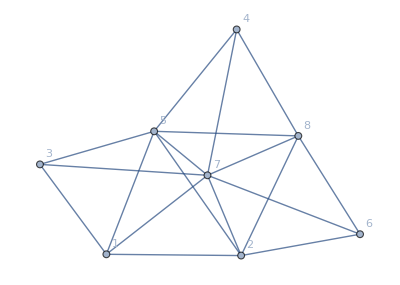
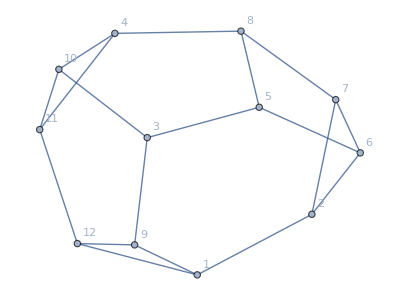
{-Graphics3D-,-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
{Graphics3D[sunny],polyhedrongraph[sunny],Graphics3D[sunnydual],polyhedrongraph[sunnydual]}
```

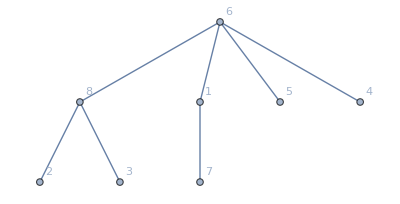

```mathematica
ClearSystemCache[]
FindSpanningTree[graph]
```

# Generating faces

```mathematica
coordinatelist = sunny[[1]];
vassoc = Merge[Join@Table[<|n -> coordinatelist[[n ]]|>,{n,1,Length[coordinatelist]}],Total]
edgeassoc =    Merge[Join@Table[<|n -> EdgeList[polyhedrongraph@sunny][[n ]]|>,{n,1,Length[EdgeList[polyhedrongraph@sunny]]}],Total]
```

<|1→{0.229834,0.697017,0.335907},2→{0.021382,0.158511,0.412443},3→{0.370203,0.865939,0.571369},4→{0.0366399,0.794312,0.755957},5→{0.0151549,0.868587,0.599216},6→{0.409509,0.0554178,0.903192},7→{0.91011,0.954531,0.69615},8→{0.0187611,0.625289,0.820292}|>

<|1→5<->7,2→4<->5,3→4<->7,4→3<->5,5→3<->7,6→2<->5,7→2<->8,8→5<->8,9→2<->7,10→6<->7,11→2<->6,12→1<->5,13→1<->2,14→1<->3,15→1<->7,16→4<->8,17→6<->8,18→7<->8|>

```mathematica
vertexlist = sunny[[2]]
```

{{7,5,4},{3,5,7},{5,2,8},{2,7,6},{2,5,1},{5,3,1},{3,7,1},{7,2,1},{5,8,4},{2,6,8},{6,7,8},{8,7,4}}

```mathematica
MeshPrimitives[BoundaryDiscretizeGraphics@sunny,2]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
coordinategroups = Table[vassoc/@vertexlist[[n]],{n, 1, Length[vertexlist]}]
```

{{{0.91011,0.954531,0.69615},{0.0151549,0.868587,0.599216},{0.0366399,0.794312,0.755957}},{{0.370203,0.865939,0.571369},{0.0151549,0.868587,0.599216},{0.91011,0.954531,0.69615}},{{0.0151549,0.868587,0.599216},{0.021382,0.158511,0.412443},{0.0187611,0.625289,0.820292}},{{0.021382,0.158511,0.412443},{0.91011,0.954531,0.69615},{0.409509,0.0554178,0.903192}},{{0.021382,0.158511,0.412443},{0.0151549,0.868587,0.599216},{0.229834,0.697017,0.335907}},{{0.0151549,0.868587,0.599216},{0.370203,0.865939,0.571369},{0.229834,0.697017,0.335907}},{{0.370203,0.865939,0.571369},{0.91011,0.954531,0.69615},{0.229834,0.697017,0.335907}},{{0.91011,0.954531,0.69615},{0.021382,0.158511,0.412443},{0.229834,0.697017,0.335907}},{{0.0151549,0.868587,0.599216},{0.0187611,0.625289,0.820292},{0.0366399,0.794312,0.755957}},{{0.021382,0.158511,0.412443},{0.409509,0.0554178,0.903192},{0.0187611,0.625289,0.820292}},{{0.409509,0.0554178,0.903192},{0.91011,0.954531,0.69615},{0.0187611,0.625289,0.820292}},{{0.0187611,0.625289,0.820292},{0.91011,0.954531,0.69615},{0.0366399,0.794312,0.755957}}}

```mathematica
EuclideanDistance[coordinategroups[[1]][[1]],coordinategroups[[1]][[2]]]
```

0.904283

```mathematica
generatepolygon[coordinates_] := 

Graphics3D@Polygon[coordinates]
```

```mathematica
generatepolygon[coordinategroups[[1]]]
```

-Graphics3D-